```mathematica
Integrate[x*n^2*E^(-1/2*x^2/a^2),{x, -Infinity, +Infinity}]
```

ConditionalExpression[0, Re[a^2]>0]

```mathematica
Integrate[N^2*2*a^2*E^(-1/2*x^2/a^2), {x, -Infinity, +Infinity}]
```

ConditionalExpression[2 √(1/a^2) a^4 N^2 √(2 π), Re[a^2]>0]

```mathematica
$Assumptions=a>0&&a∈Reals&&N∈Reals
psi[x_]:= 1/(a^2*2*Pi)^(1/4)*E^(-x^2/(4*a^2)); 
avXHat = Integrate[psi[x]*x*psi[x], {x, -Infinity, Infinity}]
avXHatSquared = Integrate[psi[x]*x^2*psi[x], {x, -Infinity, Infinity}]
deltaX = Simplify[Sqrt[avXHatSquared-avXHat]]
```

a>0&&a∈ℝ&&N∈ℝ

0

a^2

a

```mathematica
$Assumptions=a>0&&a∈Reals&&N∈Reals && hbar ∈ Reals && hbar > 0
psi[x_]:= 1/(a^2*2*Pi)^(1/4)*E^(-x^2/(4*a^2));
avPHat = Integrate[psi[x]*(hbar/I)*psi'[x], {x, -Infinity, Infinity}]
avPHatSquared = Integrate[psi[x]*(hbar^2/(-1))*psi''[x], {x, -Infinity, Infinity}]
deltaP = Sqrt[avPHatSquared-avPHat]
```

a>0&&a∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

0

hbar^2/(4 a^2)

1/2 √(hbar^2/a^2)

```mathematica
$Assumptions=a>0&&a∈Reals&&N∈Reals && hbar ∈ Reals && hbar > 0 
Simplify[deltaX*deltaP]
```

a>0&&a∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

hbar/(4 a √(2 π))

```mathematica
a hbar Ni^2 √(π/2)
```

1/(2 a √π)

hbar/(4 a √(2 π))

```mathematica
$Assumptions=a>0&&a∈Reals&&N∈Reals
psi[x_]:= 1/(a^2*2*Pi)^(1/4)*E^(-x^2/(4*a^2)); 
avXHat = Integrate[psi[x]*psi[x], {x, -Infinity, Infinity}]
```

a>0&&a∈ℝ&&N∈ℝ

1

```mathematica
Integrate[(1/(a^2*2*Pi)^(1/4))^2*x^2*E^(-x^2/(2*a^2)), {x, -Infinity, Infinity}]
```

a^2

```mathematica
$Assumptions=a>0&&a∈Reals&&N∈Reals && hbar ∈ Reals && hbar > 0
psi[x_]:= N*E^(-x^2/(4*a^2)); 
phiOfP = Integrate[psi[x]*E^(-I*p*x/hbar)/(Sqrt[2*Pi*hbar]), {x, -Infinity, Infinity}]
```

a>0&&a∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

(√2 a ⅇ^(-(a^2 p^2)/hbar^2) N)/(√hbar)

```mathematica
Integrate[phiOfP^2, {p, -Infinity, Infinity}]
```

a N^2 √(2 π)

```mathematica
$Assumptions=a>0&&a∈Reals && realASquared>0 && Element[realASquared, Reals]  &&N∈Reals && hbar ∈ Reals && hbar > 0
psi2[x_]:= N^2*E^(-(x^2/4)*(2*realASquared)/(a^4));
Solve[Integrate[psi2[x], {x, -Infinity, Infinity}]==1, N]
```

a>0&&a∈ℝ&&realASquared>0&&realASquared∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

{{N→-realASquared^(1/4)/(a (2 π)^(1/4))},{N→realASquared^(1/4)/(a (2 π)^(1/4))}}

```mathematica
$Assumptions=a>0&&a∈Reals && realASquared>0 && Element[realASquared, Reals]  &&N∈Reals && hbar ∈ Reals && hbar > 0
psi2[x_]:= ((1/a)*(realASquared/(2*Pi))^(1/4))^2*E^(-(x^2/4)*(2*realASquared)/(a^4));
xHatSquared = (Integrate[psi2[x]*x, {x, -Infinity, Infinity}])^2
xSquaredHat = Integrate[psi2[x]*x^2, {x, -Infinity, Infinity}]
deltaX = Simplify[Sqrt[xSquaredHat - xHatSquared]]
```

a>0&&a∈ℝ&&realASquared>0&&realASquared∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

0

a^4/realASquared

a^2/(√realASquared)

```mathematica
$Assumptions=a>0&&a∈Reals && realASquared>0 && Element[realASquared, Reals]  &&N∈Reals && hbar ∈ Reals && hbar > 0
psi2[x_]:= ((1/a)*(realASquared/(2*Pi))^(1/4))^2*E^(-(x^2/4)*(2*realASquared)/(a^4));
pHatSquared = (Integrate[psi2[x]*hbar/I*(-1/4)*2*x/a^2, {x, -Infinity, Infinity}])^2
pSquaredHat = Integrate[psi2[x]*hbar^2/(2*aComplex^2)*(1-x^2/(2*aComplex^2)), {x, -Infinity, Infinity}]
deltaP = Simplify[Sqrt[pSquaredHat - pHatSquared]]
```

a>0&&a∈ℝ&&realASquared>0&&realASquared∈ℝ&&N∈ℝ&&hbar∈ℝ&&hbar>0

0

-(hbar^2 (a^4-2 aComplex^2 realASquared))/(4 aComplex^4 realASquared)

1/2 hbar √(2/aComplex^2-a^4/(aComplex^4 realASquared))

```mathematica
$Assumptions=Real[a]>0&&a∈Complexes
Simplify[hbar/2*  Sqrt[2/a^2-Abs[a]^4/(a^4* Real[a^2])]]
```

Real[a]>0&&a∈ℂ

1/2 hbar √(2/a^2-Abs[a]^4/(a^4 Real[a^2]))

```mathematica
$Assumptions=a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]
psi[x_]:= N*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(-I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);
psiConjugate[x_]:= N*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);
Solve[Integrate[psiConjugate[x]*psi[x],{x, 0, a}]==1, N]
```

m (a>0&&a∈ℝ&&n≥1&&n∈ℤ&&hbar>0&&hbar∈ℝ&&t∈ℝ&)>0&&m∈ℝ

{{N→-2/(√(2 a-(a Sin[2 n π])/(n π)))},{N→2/(√(2 a-(a Sin[2 n π])/(n π)))}}

```mathematica
$Assumptions=a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]
psi[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I);
xHat = FullSimplify[Integrate[psi[x]*x*psi[x],{x, 0, a}], Assumptions -> Element[n, Integers]]
xSquaredHat = FullSimplify[Integrate[psi[x]*x^2*psi[x],{x, 0, a}],Assumptions -> Element[n, Integers]]
deltaX =FullSimplify[Sqrt[xSquaredHat - xHat^2]]
```

m (a>0&&a∈ℝ&&n≥1&&n∈ℤ&&hbar>0&&hbar∈ℝ&&t∈ℝ&)>0&&m∈ℝ

a/2

1/6 a^2 (2-3/(n^2 π^2))

(√(a^2 (1-6/(n^2 π^2))))/(2 √3)

```mathematica
$Assumptions=a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]
psi[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I);
pHat = FullSimplify[Integrate[psi[x]*hbar/I*psi'[x],{x, 0, a}], Assumptions -> Element[n, Integers]]
pSquaredHat = FullSimplify[-Integrate[psi[x]*hbar^2*psi''[x],{x, 0, a}],Assumptions -> Element[n, Integers]]
deltaP =FullSimplify[Sqrt[pSquaredHat - pHat^2], Assumptions->a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]]
```

m (a>0&&a∈ℝ&&n≥1&&n∈ℤ&&hbar>0&&hbar∈ℝ&&t∈ℝ&)>0&&m∈ℝ

0

(hbar^2 n^2 π^2)/a^2

√((hbar^2 n^2)/a^2) π

```mathematica
deltaXdeltaP =FullSimplify[deltaP*deltaX, Assumptions->a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]]
```

(√((hbar^2 n^2)/a^2) √(a^2 (-6/n^2+π^2)))/(2 √3)

```mathematica
deltaP*deltaX-hbar/2
```

-hbar/2+(√((hbar^2 n^2)/a^2) √(a^2 (1-6/(n^2 π^2))) π)/(2 √3)

```mathematica
FullSimplify[-hbar/2+(√((hbar^2 n^2)/a^2) √(a^2 (1-6/(n^2 π^2))) π)/(2 √3), Assumptions->a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]]
```

1/6 (-3 hbar+√3 √((hbar^2 n^2)/a^2) √(a^2 (-6/n^2+π^2)))

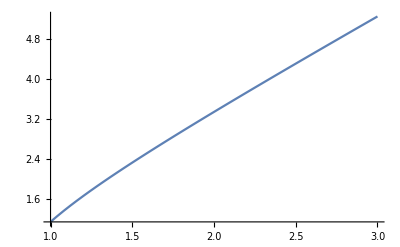

```mathematica
Plot[Sqrt[(x^2*Pi^2-6)/3], {x, 1,3}]
```

```mathematica
N@Sqrt[(1^2*Pi^2-6)/3]
```

1.13572

```mathematica
$Assumptions=a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]
psi[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(-I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);psiConjugate[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);
xHat = FullSimplify[Integrate[psiConjugate[x]*x*psi[x],{x, 0, a}], Assumptions -> Element[n, Integers]]
xSquaredHat = FullSimplify[Integrate[psiConjugate[x]*x^2*psi[x],{x, 0, a}],Assumptions -> Element[n, Integers]]
deltaX =FullSimplify[Sqrt[xSquaredHat - xHat^2]]
```

m (a>0&&a∈ℝ&&n≥1&&n∈ℤ&&hbar>0&&hbar∈ℝ&&t∈ℝ&)>0&&m∈ℝ

a/2

1/6 a^2 (2-3/(n^2 π^2))

(√(a^2 (1-6/(n^2 π^2))))/(2 √3)

```mathematica
$Assumptions=a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]
psi[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(-I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);psiConjugate[x_]:= Sqrt[2/a]*(E^(I*n*Pi*x/a)-E^(-I*n*Pi*x/a))/(2*I)*E^(I*(hbar*Pi^2*n^2)/(2*m*a^2)*t);
pHat = FullSimplify[Integrate[psiConjugate[x]*hbar/I*psi'[x],{x, 0, a}], Assumptions -> Element[n, Integers]]
pSquaredHat = FullSimplify[-Integrate[psiConjugate[x]*hbar^2*psi''[x],{x, 0, a}],Assumptions -> Element[n, Integers]]
deltaP =FullSimplify[Sqrt[pSquaredHat - pHat^2], Assumptions->a>0&&a∈Reals && n>=1 && Element[n, Integers] && hbar >0 && Element[hbar, Reals] && Element[t, Reals] & m > 0 && Element[m, Reals]]
```

m (a>0&&a∈ℝ&&n≥1&&n∈ℤ&&hbar>0&&hbar∈ℝ&&t∈ℝ&)>0&&m∈ℝ

0

(hbar^2 n^2 π^2)/a^2

√((hbar^2 n^2)/a^2) π

∫_0^a 1/a^2 2 ⅇ^(-1/2 ⅈ n π ((hbar n π t+2 a m x)/(a^2 m)-(n π Conjugate[hbar] Conjugate[t])/(Conjugate[a]^2 Conjugate[m]))) hbar n π Cos[(n π x)/a]^2 Sign[a] Sin[(n π Conjugate[x])/Conjugate[a]] (-ⅈ+Tan[(n π x)/a])ⅆx

(hbar^2 n^2 π^2)/a^2